```mathematica
func[x_]:=Log[Exp[x]-1]
```

```mathematica
<<FunctionApproximations`
```

```mathematica
x0=0
x1=0.001
x2=0.01
x3=0.1
x4=1.0
```

0

0.001

0.01

0.1

1.

```mathematica
approx1=RationalInterpolation[func[x],{x,5,5},{x,x1,x2}]
```

(-10.1609-49897.2 x-3.85567×10^7 x^2-6.7778×10^9 x^3-2.42199×10^11 x^4-3.56101×10^11 x^5)/(1+6487.9 x+6.29479×10^6 x^2+1.43337×10^9 x^3+7.6707×10^10 x^4+6.06654×10^11 x^5)

```mathematica
approx2=RationalInterpolation[func[x],{x,5,5},{x,x2,x3}]
```

(-7.84579-3428.78 x-228752. x^2-3.08203×10^6 x^3-3.83627×10^6 x^4+1.22519×10^7 x^5)/(1+638.731 x+60430.9 x^2+1.31543×10^6 x^3+6.37306×10^6 x^4+3.39142×10^6 x^5)

```mathematica
approx3=RationalInterpolation[func[x],{x,5,5},{x,x3,x4}]
```

(-5.75178-261.588 x-1610.19 x^2-291.612 x^3+3733.96 x^4+1224.21 x^5)/(1+79.5298 x+953.457 x^2+2638.61 x^3+1506.96 x^4-27.3356 x^5)

```mathematica
fullapprox[x_]:=If[x>x4,func[x],If[x>x3,approx3,func[x]]]
```

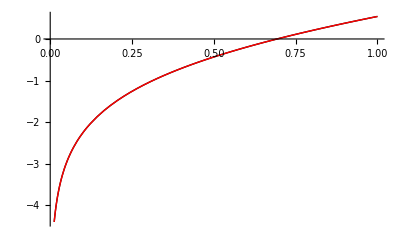

```mathematica
Plot[{func[x],fullapprox[x]},{x,x1,x4},PlotStyle->{Black,Red}]
```

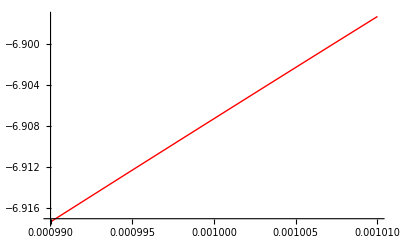

```mathematica
Plot[fullapprox[x],{x,0.99*x1,1.01*x1},PlotStyle->{Black,Red}]
```

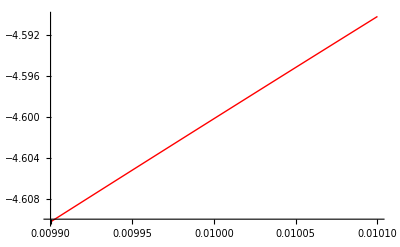

```mathematica
Plot[fullapprox[x],{x,0.99*x2,1.01*x2},PlotStyle->{Black,Red}]
```

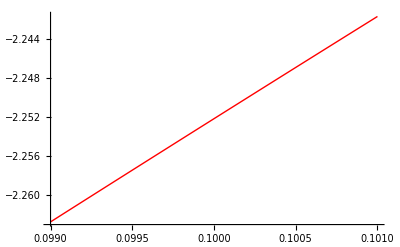

```mathematica
Plot[fullapprox[x],{x,0.99*x3,1.01*x3},PlotStyle->{Black,Red}]
```

```mathematica
adiff[x_]:=fullapprox[x]-func[x]
```

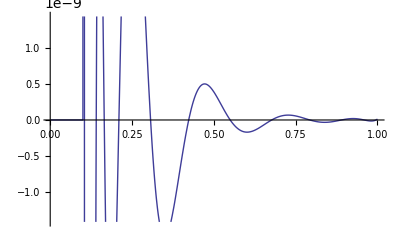

```mathematica
Plot[adiff[x],{x,x1,x4}]
```

```mathematica
pdiff[x_]:=100*(fullapprox[x]-func[x])/func[x]
```

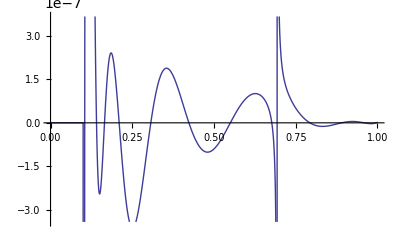

Plot[pdiff[x],{x,x,x4}]

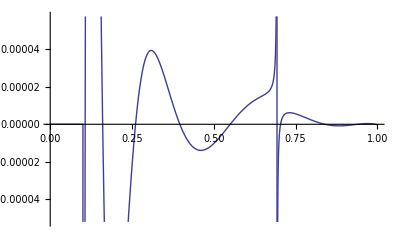

```mathematica
Plot[pdiff[x],{x,x0,x4}]
```

```mathematica
CForm[approx1]
```

(-10.160864271837852 - 49897.232955349435*x - 
     3.8556691413516626e7*Power(x,2) - 
     6.777802187903648e9*Power(x,3) - 
     2.4219870520951263e11*Power(x,4) - 
     3.561013055572104e11*Power(x,5))/
   (1 + 6487.897680328305*x + 6.294785929296415e6*Power(x,2) + 
     1.433365885358317e9*Power(x,3) + 
     7.670700146255556e10*Power(x,4) + 
     6.066541645606035e11*Power(x,5))

```mathematica
CForm[approx2]
```

(-7.8457884996762886 - 3428.7803682618655*x - 
     228752.19522200784*Power(x,2) - 
     3.082031951315743e6*Power(x,3) - 
     3.836269866611495e6*Power(x,4) + 
     1.2251899637889972e7*Power(x,5))/
   (1 + 638.7306744821685*x + 60430.91566706335*Power(x,2) + 
     1.3154320245552924e6*Power(x,3) + 
     6.373056425285323e6*Power(x,4) + 
     3.3914173865251006e6*Power(x,5))

```mathematica
CForm[approx3]
```

(-5.751779352669391 - 261.58792019175337*x - 
     1610.1902844993492*Power(x,2) - 291.611754211725*Power(x,3) + 
     3733.9573380993666*Power(x,4) + 1224.21046268194*Power(x,5))/
   (1 + 79.52981220030104*x + 953.4570585801343*Power(x,2) + 
     2638.6098827046494*Power(x,3) + 
     1506.9612671002426*Power(x,4) - 27.3355820759903*Power(x,5))